```mathematica
(* clear memory *)
ClearAll["Global`*"]
```

```mathematica
(* Declare TDOS function that take the eigenvalue list and Gaussian width as inputs and returns TDOS as a function of energy *)
TDOS[Energy_,Eigenvalues_,Gwidth_]:=Apply[Plus,1/(Sqrt[2Pi]Gwidth)Exp[-(Energy-Eigenvalues)^2/(2 Gwidth^2)]];
```

```mathematica
(* Read orbital eigenvalues, in this example MOs.txt have three columns. If it contains more or less columns, change the size of the array in the second argument *)
Data1=ReadList["/home/zhenzhe/Desktop/mols_MOs/indacene-MOs.txt",{Number,Number,Number,String}];
Data2=ReadList["/home/zhenzhe/Desktop/mols_MOs/coranene-MOs.txt",{Number,Number,Number,String}];
(* Use the second column *)
(*Data1*)
OrbitalEnergies=Data1[[All,3]];
OrbitalEnergies2=Data2[[All,3]];
(*OrbitalEnergiesz*)
Length[OrbitalEnergies]
Length[OrbitalEnergies2]
OrbitalEnergies=OrbitalEnergies*27.2114
OrbitalEnergies2=OrbitalEnergies2*27.2114
```

590

592

{663.085,662.648,662.647,662.164,661.553,661.552,660.958,660.957,660.827,660.339,660.339,660.032,655.434,655.433,653.899,653.898,653.622,652.947,651.275,651.275,650.304,648.003,648.003,639.576,138.853,134.701,134.498,134.497,131.55,130.868,130.868,123.374,123.374,119.909,119.908,118.857,114.323,114.261,114.261,112.51,111.685,111.684,110.288,109.009,109.009,106.304,104.283,104.282,102.718,101.953,101.952,99.7559,99.7554,99.656,98.8713,98.8704,98.3847,97.6633,97.6633,96.7109,96.109,95.7232,95.7232,94.3789,94.3778,93.7316,93.7308,93.3114,92.0396,91.7476,91.747,91.368,90.59,89.4792,89.4787,89.448,88.9998,87.178,86.8914,86.8912,86.1184,86.1181,85.7129,85.7126,85.6215,84.483,84.4824,84.4468,84.3668,84.3668,83.6688,83.3156,82.2222,82.2222,81.3147,81.2502,81.2502,80.1362,80.0135,80.0135,79.9577,79.9574,79.3354,79.3318,79.3316,78.4543,78.4537,78.4382,78.2956,77.6153,77.4782,77.4782,77.4502,77.3016,77.3016,76.7862,76.7157,76.7157,76.3506,76.3503,75.695,75.144,75.144,74.7617,74.7617,74.6139,74.4945,74.4945,74.2607,74.1059,72.9317,72.763,72.7627,72.2664,70.5518,70.5518,70.1475,70.1469,69.7621,69.2087,69.0585,69.0579,68.1613,68.1597,67.9643,67.5684,66.6432,66.6426,64.6439,64.4456,64.4453,64.057,63.8162,63.8156,63.7797,62.8643,62.8638,61.4654,61.3435,61.3429,60.9584,60.9582,60.7821,60.6594,60.0659,60.0654,59.6493,59.5307,59.2536,59.2531,57.8855,57.8852,57.6871,57.6868,57.4084,57.3287,57.3282,56.9467,56.9464,56.1611,55.7426,55.5311,55.4623,55.4623,54.7216,54.7213,54.635,54.6348,54.1063,54.1061,53.8563,53.0206,52.9896,52.9896,52.6364,52.6361,52.1501,51.9169,51.9166,51.5123,51.1803,51.1112,51.1104,51.0551,50.4276,50.3229,50.3229,50.0488,50.0486,49.6306,49.2973,49.2967,48.9076,48.6812,48.6809,48.2445,47.6425,47.5495,47.5492,47.0923,47.0923,46.8439,46.1459,46.0855,46.0855,46.0074,46.0074,44.9421,44.7924,44.7911,44.6972,44.3208,44.3206,44.3149,44.2316,44.2313,43.6857,42.7725,42.7722,42.6297,42.6294,42.3584,42.0778,41.9426,41.9423,41.2661,41.2653,41.0642,38.4581,38.4579,38.2527,37.4758,36.9302,36.93,36.5079,36.5076,36.3786,35.3786,34.6126,34.6124,34.5612,33.6298,33.6295,33.3903,33.3903,32.9111,32.7378,32.7359,32.7356,32.6259,32.6257,32.3144,32.1963,31.8893,31.8893,30.9622,30.9015,30.9015,30.5492,30.5492,30.2637,29.9189,29.8727,29.8724,29.7407,29.7404,29.6988,29.5078,29.3777,29.3774,29.3676,29.3674,29.0014,29.0014,28.6675,28.6672,28.6533,28.4471,27.8133,27.5564,27.5371,27.5371,27.3379,27.2607,27.2604,26.9431,26.3959,26.3956,26.0519,25.9896,25.9896,25.6269,25.4242,25.2307,25.2307,24.9784,24.9784,24.4037,24.1049,24.1047,24.0682,23.4189,23.3732,23.373,23.0358,22.8505,22.8502,22.5463,22.5463,22.432,22.4317,22.3514,22.0543,22.0543,21.7525,21.7239,21.7239,21.4197,20.9765,20.9765,20.9713,20.6812,20.3043,20.0216,19.7299,19.7299,19.6415,19.6412,19.5032,19.5032,19.2583,19.0249,19.0249,19.0126,18.9484,18.9484,18.7808,18.7805,18.5927,18.3571,18.3571,18.2205,18.2202,18.1704,17.7734,17.5992,17.55,17.3848,17.3848,17.147,16.8014,16.8014,16.4335,16.4335,16.3981,16.3979,16.3897,16.0267,15.4814,15.4474,15.4471,14.7167,14.7165,14.4539,14.0011,14.0008,13.5317,12.9148,12.9145,12.9145,12.5191,12.5191,12.3744,12.2949,12.2947,11.7458,11.6908,11.6908,11.5093,11.2296,11.2296,10.9929,10.8179,10.8179,10.7123,10.7123,10.6848,10.4647,10.4644,10.4516,10.3001,10.3001,9.97162,9.86604,9.82195,9.79774,9.79746,9.63937,9.55311,9.31718,9.31691,9.20725,9.20725,9.16045,9.16045,8.93323,8.93296,8.81921,8.66493,8.65295,8.65268,8.57513,8.28533,7.86709,7.86682,7.67253,7.65865,7.56803,7.56803,7.33211,7.33211,7.2747,7.2747,7.20993,7.19714,7.19714,7.18789,6.89319,6.89319,6.70298,6.57781,6.57781,6.56203,6.35141,6.35141,6.28719,6.26461,6.26461,6.25182,6.25182,5.89916,5.88066,5.83548,5.83548,5.50459,5.50459,5.0801,5.0801,4.98731,4.96962,4.96962,4.84798,4.84363,4.84363,4.81941,4.57886,4.57886,4.53532,4.50866,4.35845,4.35818,4.35818,4.14675,4.06538,4.06538,3.95627,3.72089,3.72089,3.53558,3.4436,3.4436,3.05475,3.05475,2.96441,2.96441,2.80495,2.68141,2.28821,2.28821,1.82017,1.8052,1.57255,1.50016,1.49989,1.43948,1.43948,1.13907,1.13907,1.04111,0.909133,-1.39921,-1.39948,-6.67904,-6.67904,-9.09459,-9.15419,-9.15419,-9.67501,-11.0261,-11.0263,-11.3687,-11.4742,-11.4742,-12.1665,-12.1665,-12.1989,-12.5894,-12.5896,-12.5962,-12.9009,-13.0013,-13.0016,-13.7662,-13.7665,-13.776,-14.3442,-14.3595,-14.3595,-14.5355,-15.4327,-15.4329,-15.5943,-16.1609,-16.5794,-16.5796,-17.1524,-17.1527,-18.473,-18.8926,-18.8926,-19.227,-19.2883,-21.1563,-21.1563,-21.7223,-21.7223,-23.3523,-23.3526,-23.7063,-23.749,-25.0843,-25.25,-25.25,-26.7464,-26.7466,-27.8473,-279.795,-279.795,-279.795,-280.122,-280.124,-280.124,-280.223,-280.224,-280.225,-280.495,-280.495,-280.495,-280.522,-280.522,-280.522,-280.527,-280.527,-280.527,-280.565,-280.565,-280.565,-280.568,-280.568,-280.568}

{662.456,662.321,662.195,662.194,662.17,662.169,659.341,658.319,658.319,657.91,657.91,657.114,656.69,656.208,656.208,655.747,655.746,653.753,653.612,652.802,652.801,648.491,648.49,639.796,140.755,135.846,135.016,135.016,134.953,134.953,134.506,124.599,124.599,119.79,119.789,117.519,115.114,114.592,114.592,114.52,113.888,113.888,112.158,109.283,109.282,107.235,104.497,104.497,103.022,102.612,102.612,101.228,101.228,100.827,99.8103,98.9654,98.6266,98.6266,97.693,97.6925,97.2522,97.2519,96.5199,96.3722,96.241,96.0051,96.0051,94.2965,94.2962,93.2527,93.2524,92.5729,91.4053,91.4053,91.0844,91.0842,90.1614,90.0403,89.7614,87.8871,87.8115,87.8115,86.8084,86.4449,86.4449,85.7298,82.7539,82.7537,82.6182,82.6179,81.9994,81.8854,81.2086,81.2083,81.1923,81.1917,80.8355,80.8353,80.6913,80.6913,80.0298,79.5863,79.2393,79.2391,78.8905,78.8897,78.6956,78.5822,77.9231,77.9231,77.6777,77.66,77.5805,77.5726,77.5726,77.4118,77.4118,77.2496,77.0986,77.0986,76.6668,76.6597,76.6597,76.2159,75.1168,75.1168,74.4079,74.227,74.0719,73.212,73.2117,72.5461,72.5459,71.4607,71.4607,71.2903,71.2588,71.2503,71.2501,70.6705,69.8008,67.924,67.924,66.9414,66.6998,66.6998,66.3433,66.343,65.5144,65.5144,65.1487,64.8703,64.8701,63.6837,62.5402,62.54,61.9402,61.7655,61.1876,61.187,60.9141,60.9138,60.3663,60.3663,59.7913,59.5717,59.5715,59.4275,59.4272,58.2245,58.2242,58.2095,58.1421,57.8014,57.1736,57.1733,57.0868,56.8911,56.8909,56.606,56.5801,56.3339,56.3257,55.0127,54.8661,54.8661,54.6195,54.6193,54.3556,54.2691,54.2691,53.9281,53.9278,53.6277,53.0192,53.019,52.9273,52.7017,52.7014,52.3147,52.1754,52.1754,50.9008,50.9003,50.2061,50.2058,49.7566,49.7563,49.7389,49.7386,49.5171,49.5169,49.2388,49.1756,48.7473,48.5013,47.8474,47.8474,46.7511,46.7508,46.3535,45.9933,45.953,45.9527,45.6615,45.6267,45.6264,45.1032,45.1029,45.0411,44.3097,44.301,44.3007,44.1736,43.2539,43.2539,43.049,43.0441,43.0438,42.7575,42.68,42.4895,42.4895,42.1926,42.1875,42.1872,42.1496,42.1494,41.7828,41.3768,41.3766,39.9629,39.6108,38.5172,38.469,38.469,37.8377,37.8375,35.223,35.2227,34.3487,34.2689,34.1653,34.165,34.0948,34.0945,33.7187,33.7187,33.1786,33.1783,32.2648,32.1203,32.0686,31.7712,31.1617,31.1617,31.1399,30.6458,30.6455,30.4441,30.4438,30.3979,29.6251,29.6248,29.4906,29.4898,29.3668,29.3657,29.2669,29.2667,29.1165,29.1162,28.6286,28.5839,28.5535,28.5535,28.3282,28.305,28.305,28.2158,28.0536,28.0533,27.6386,27.1254,27.1254,27.0457,26.9469,26.7491,26.7488,26.7447,26.2438,26.1847,25.9978,25.5518,25.0154,25.0154,24.7953,24.7953,24.5128,24.1871,23.8611,23.5926,23.5926,23.5357,23.5354,23.4603,23.4603,23.4081,23.1422,23.1419,22.8241,22.8238,22.4021,22.3955,22.3953,21.5993,20.7794,20.7794,20.5506,20.5506,20.4262,20.4262,20.266,20.2521,20.2518,20.0023,19.9786,19.9593,19.8232,19.5476,19.5476,19.3313,19.2197,19.2194,18.9541,18.9541,18.9212,18.8627,18.8627,18.7424,18.7421,18.414,18.414,18.3263,18.1813,17.6509,17.6322,17.6322,17.5677,17.3546,17.3546,17.2368,17.2368,16.6547,16.6547,16.289,16.1508,16.0977,16.0977,15.8866,15.8863,15.6675,15.5116,14.9235,14.3497,13.9812,13.6898,13.6895,13.3336,13.3336,12.9061,12.9058,12.5643,12.564,12.1368,11.9953,11.9412,11.5959,11.588,11.588,11.1085,11.1085,10.9227,10.9224,10.8598,10.8029,10.8029,10.681,10.6807,10.6587,10.6587,10.6527,10.1172,10.0679,9.98958,9.98958,9.98849,9.80427,9.73352,9.73352,9.71501,9.57324,9.57297,9.43229,9.43202,9.38929,9.26303,9.26167,9.2614,8.83581,8.83554,8.81051,8.57431,8.57404,8.16913,8.16913,8.10029,8.03716,7.73947,7.68831,7.68831,7.67198,7.67198,7.49973,7.41728,7.32123,7.32123,7.27823,7.10326,7.10326,7.08612,7.08612,6.79033,6.79033,6.75169,6.59822,6.59822,6.43277,6.43277,6.16855,6.16855,6.0159,5.80474,5.42432,5.42405,5.41262,5.41262,5.35929,5.35929,5.12608,5.12608,4.98758,4.90622,4.84853,4.77261,4.70676,4.69315,4.58839,4.58839,4.49804,4.49804,4.19627,4.18811,4.18811,4.17695,4.17695,3.99953,3.63898,3.56524,3.56524,3.41449,3.41449,3.02836,3.02808,3.02808,2.90863,2.87815,2.87815,2.61828,2.33828,2.33828,2.32739,1.84847,1.83568,1.50751,1.45445,1.45445,1.17608,1.17608,1.07186,1.07186,1.05308,-0.139594,-0.139594,-7.45103,-7.45103,-9.04616,-9.04643,-9.49188,-9.70277,-10.9297,-10.9297,-11.0105,-11.5153,-11.5153,-12.176,-12.176,-12.1763,-12.5608,-12.6073,-13.126,-13.126,-13.4081,-13.4081,-13.834,-13.9605,-13.9608,-14.1679,-14.3502,-14.9361,-14.9363,-15.0381,-15.0381,-15.5151,-15.5151,-16.7043,-17.3097,-17.3293,-17.3293,-17.8428,-17.959,-19.799,-19.9506,-19.9509,-20.0945,-20.0945,-22.2478,-22.2478,-23.1539,-23.1542,-23.6154,-24.0511,-24.8916,-25.3798,-25.3798,-26.7025,-26.7025,-27.7216,-280.149,-280.15,-280.15,-280.15,-280.15,-280.15,-280.169,-280.169,-280.169,-280.169,-280.169,-280.169,-280.382,-280.386,-280.386,-280.39,-280.39,-280.391,-280.399,-280.4,-280.4,-280.408,-280.408,-280.413}

```mathematica
GaussWidth=0.2;
TDOS1=TDOS[Ex,OrbitalEnergies,GaussWidth];
(* TDOS1 is now a smooth function of Ex *)

TDOS2=TDOS[Ex,OrbitalEnergies2,GaussWidth];
```

General::munfl: Exp[-5.83255×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.82509×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.82508×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

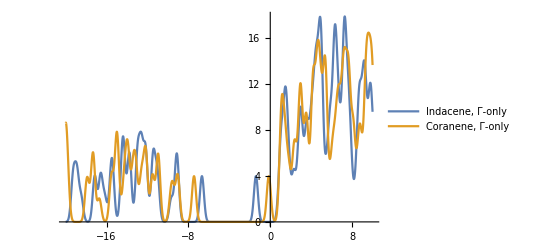

```mathematica
(* Plot two DOS functions. They are the same in this example *)
Emin=-20;
Emax=10;
Plot1=Plot[{TDOS1,TDOS2},{Ex,Emin,Emax},PlotRange->All,PlotLegends->{"Indacene, Γ-only","Coranene, Γ-only"}]
```